```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
HotQCDp=Flatten[Import["../../../fluctuations_T/LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../fluctuations_T/LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../fluctuations_T/LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../fluctuations_T/LQCDdata/hotdpt4u.dat"]];
Tcl=156;
Hotpdown=Transpose[{HotQCDT,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../fluctuations_T/LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../fluctuations_T/LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../fluctuations_T/LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT,WBp-WBdp}];
WBup=Transpose[{WBT,WBp+WBdp}];
WBcs=Table[Import["../../../fluctuations_T/LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../fluctuations_T/LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT,WBcs-WBcserr}];
```

```mathematica
mub={0,50,100,200,300,400,500,550,600};
chi0data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi0.dat"]],{i,1,Length[mub]}];
chi1data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi1.dat"]],{i,1,Length[mub]}];
chi2data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi2.dat"]],{i,1,Length[mub]}];
chi3data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi3.dat"]],{i,1,Length[mub]}];
chi4data=Table[Flatten[Import["./MUB"<>ToString[mub[[i]]]<>"/data/chi4.dat"]],{i,1,Length[mub]}];
T=Table[10+2i,{i,1,125}];
poT4data=Table[Transpose[{T,chi0data[[i]]/T^4}],{i,1,Length[mub]}];
c1data=Table[Transpose[{T,chi1data[[i]]}],{i,1,Length[mub]}];
c2data=Table[T^2 chi2data[[i]]^-1,{i,1,Length[mub]}];
c2dataplot=Table[Transpose[{T,c2data[[i]]}],{i,1,Length[mub]}];
```

```mathematica
(*c1=chi1;
c2=T^2(1/chi2)^1;
c3=-T^5(1/chi2)^3(chi3);
c4=T^8(3(1/chi2)^5(chi3)^2-(1/chi2)^4 chi4);
c5=T^11(-15(1/chi2)^7(chi3)^3-(1/chi2)^5 chi5+10(1/chi2)^6 chi3 chi4);
c6=T^14(105(1/chi2)^9 chi3^4-105(1/chi2)^8 chi3^2 chi4+10(1/chi2)^7 chi4^2+15(1/chi2)^7 chi3 chi5-(1/chi2)^6 chi6);*)
```

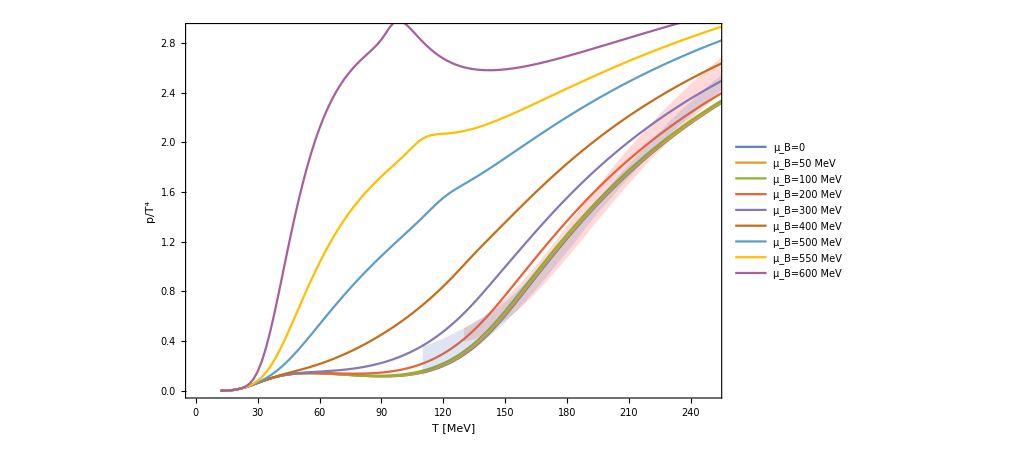

```mathematica
Show[ListLinePlot[{Hotpdown,Hotpup},Filling->{1->{2}},FillingStyle->LightRed,PlotStyle->{None,None}],ListLinePlot[poT4data,PlotLegends->{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=200 MeV","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV"}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],PlotRange->{{0,250},{0,2.9}},AxesOrigin->{0,0.},Frame->True,FrameLabel->{Style[" T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["p/T^4",Black,15,FontFamily->"Times New Roman"]}]
```

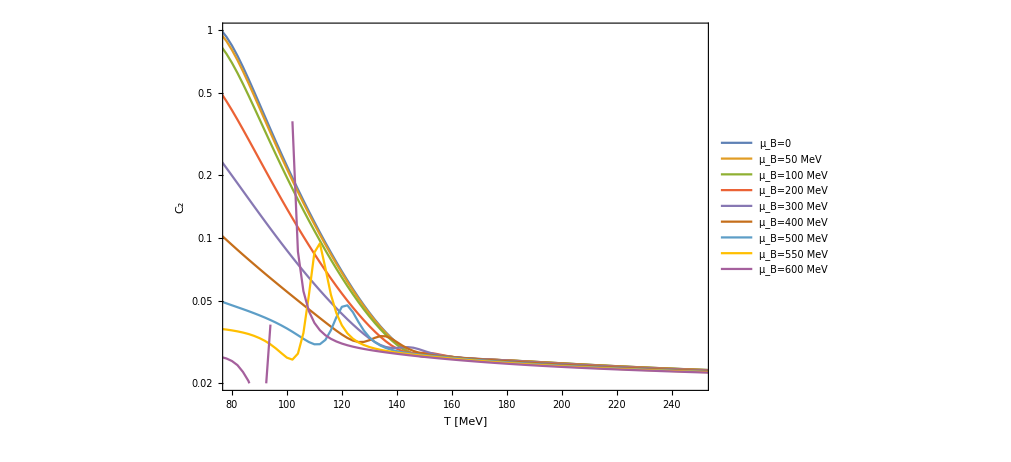

```mathematica
ListLinePlot[c2dataplot,PlotLegends->{"μ_B=0","μ_B=50 MeV","μ_B=100 MeV","μ_B=200 MeV","μ_B=300 MeV","μ_B=400 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV"},PlotRange->{{80,250},{0.02,1.}},ScalingFunctions->{Automatic,"Log"},Frame->True,FrameLabel->{Style[" T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["C_2",Black,15,FontFamily->"Times New Roman"]}]
```

### Freeze-out line

```mathematica
STARFitI=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitI.dat"]]}];
STARFitII=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitII.dat"]]}];
TI=Table[Interpolation[STARFitI][mub[[i]]],{i,2,Length[mub]}];
TII=Table[Interpolation[STARFitII][mub[[i]]],{i,2,Length[mub]}];
c2foI=Table[{sqrts[mub[[i]]],(intfun[[i]][TI[[i-1]]])/((*TI[[i-1]]*)1)},{i,2,Length[mub]}];
c2foII=Table[{sqrts[mub[[i]]],(intfun[[i]][TII[[i-1]]])/((*TII[[i-1]]*)1)},{i,2,Length[mub]}];
```

```mathematica
mubfo[sqrts_]:=1307.5/(1+0.288 sqrts);
sqrts[muB_]:=-(1.7361111111111112 (-2615.+2. muB))/muB;
Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/muB-1)/0.288]/0.45])+6;
```

```mathematica
sqrts[mub[[2;;-1]]]
```

{87.3264,41.9271,19.2274,11.6609,7.8776,5.60764,4.7822,4.09433}

```mathematica
Tfo[mub[[2;;-1]]]
```

{164.296,163.873,161.465,155.806,145.296,128.612,117.88,105.801}

```mathematica
data=Table[Transpose[{T,c2data[[i]]}],{i,1,Length[mub]}];
intfun=Table[Interpolation[data[[i]]],{i,1,Length[mub]}];
c2fo=Table[{sqrts[mub[[i]]],(intfun[[i]][Tfo[mub[[i]]]])/((*Tfo[mub[[i]]]*)1)},{i,2,Length[mub]}];
```

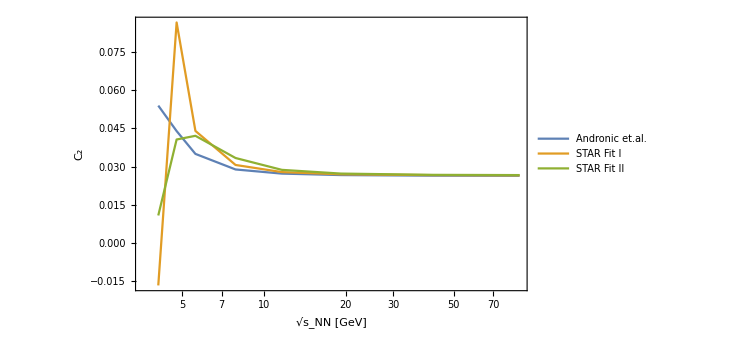

```mathematica
ListLinePlot[{c2fo,c2foI,c2foII},PlotRange->All,ScalingFunctions->{"Log",Automatic},PlotLegends->{"Andronic et.al.","STAR Fit I","STAR Fit II"},Frame->True,FrameLabel->{Style["√s_NN [GeV]",Black,15,FontFamily->"Times New Roman"],Style["C_2",Black,15,FontFamily->"Times New Roman"]}]
```